## Aligned potentials, starting from the same minimum

Using τ = τ0 exp(β E), τ0 cancels when looking at ratios

```mathematica
Energy[x_,y_]:=Eo/2(1-Cos[3(x-ϕ)])+E1/2(1-Cos[3y])+Ecouple/2(1-Cos[x-y])-ψo x+ψ1 y
```

```mathematica
Energy[x,y]/.ϕ->0
```

y ψ1-x ψo+1/2 Eo (1-Cos[3 x])+1/2 Ecouple (1-Cos[x-y])+1/2 E1 (1-Cos[3 y])

```mathematica
EFoFa=(Energy[π/3,0]-Energy[0,0])/.ϕ->0
```

Ecouple/4+Eo-(π ψo)/3

```mathematica
EFoBa=(Energy[-π/3,0]-Energy[0,0])/.ϕ->0
```

Ecouple/4+Eo+(π ψo)/3

```mathematica
EF1Fa=(Energy[0,π/3]-Energy[0,0])/.ϕ->0
```

E1+Ecouple/4+(π ψ1)/3

```mathematica
EF1Ba=(Energy[0,-π/3]-Energy[0,0])/.ϕ->0
```

E1+Ecouple/4-(π ψ1)/3

```mathematica
Exp[EFoF]/Exp[EF1B]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

```mathematica
Exp[EF1F]/Exp[EFoB]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

```mathematica
Exp[EF1F]/Exp[EFoF]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1+ψo))

```mathematica
Exp[EFoB]/Exp[EF1B]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1+ψo))

```mathematica
tf=1/(1/Exp[EF1F]+1/Exp[EFoF])/.Eo->E1//Simplify;
```

```mathematica
tb=1/(1/Exp[EF1B]+1/Exp[EFoB])/.Eo->E1//Simplify;
```

```mathematica
tf/tb//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

tFoF/tF1B=  tF1F/tFoB= exp(1/3 β π(ψ1-ψo))

tF1F/tFoF=  tFoB/tF1B= exp(1/3 β π(ψ1+ψo))

tF/tB= exp(1/3 β π(ψ1-ψo))

## Aligned potentials, starting from the neighbouring minima

Using τ = τ0 exp(β E), τ0 cancels when looking at ratios

```mathematica
Energy[x_,y_]:=Eo/2(1-Cos[3(x-ϕ)])+E1/2(1-Cos[3y])+Ecouple/2(1-Cos[x-y])-ψo x+ψ1 y
```

```mathematica
Energy[x,y]/.ϕ->0
```

y ψ1-x ψo+1/2 Eo (1-Cos[3 x])+1/2 Ecouple (1-Cos[x-y])+1/2 E1 (1-Cos[3 y])

```mathematica
EFoFb=(Energy[π,0]-Energy[ 2π/3,0])/.ϕ->0
```

Ecouple/4+Eo-(π ψo)/3

```mathematica
EFoB=(Energy[π/3,0]-Energy[2π/3,0])/.ϕ->0
```

-Ecouple/2+Eo+(π ψo)/3

```mathematica
EF1F=(Energy[2π/3,π/3]-Energy[2π/3,0])/.ϕ->0
```

E1-Ecouple/2+(π ψ1)/3

```mathematica
EF1B=(Energy[2π/3,-π/3]-Energy[2π/3,0])/.ϕ->0
```

E1+Ecouple/4-(π ψ1)/3

```mathematica
Exp[EFoF]/Exp[EF1B]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

```mathematica
Exp[EF1F]/Exp[EFoB]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

```mathematica
Exp[EF1F]/Exp[EFoF]/.Eo->E1//Simplify
```

ⅇ^(-(3 Ecouple)/4+1/3 π (ψ1+ψo))

```mathematica
Exp[EFoB]/Exp[EF1B]/.Eo->E1//Simplify
```

ⅇ^(-(3 Ecouple)/4+1/3 π (ψ1+ψo))

```mathematica
tf=1/(1/Exp[EF1F]+1/Exp[EFoF])/.Eo->E1//Simplify;
```

```mathematica
tb=1/(1/Exp[EF1B]+1/Exp[EFoB])/.Eo->E1//Simplify;
```

```mathematica
tf/tb//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

```mathematica
Exp[-EF1F]
```

ⅇ^(-E1+Ecouple/2-(π ψ1)/3)

```mathematica
Exp[-EFoF]
```

ⅇ^(-Ecouple/4-Eo+(π ψo)/3)

tFoF/tF1B=  tF1F/tFoB= exp(1/3 β π(ψ1-ψo))

tF1F/tFoF=  tFoB/tF1B = exp(β(1/3 π(ψ1 + ψo)-3/4 Ecouple))

tF/tB= exp(1/3 β π(ψ1-ψo))

### Trying out some ratios and rates

```mathematica
kf11=1/(Exp[EFoFa]+Exp[EF1F])/.Eo->E1/.{ψo->-2,ψ1->4,E1->2}//Simplify
```

1/(ⅇ^(2+Ecouple/4+(2 π)/3)+ⅇ^(2-Ecouple/2+(4 π)/3))

```mathematica
kft=Exp[-EFoFa]+Exp[-EF1Fa]/.Eo->E1/.{ψo->-2,ψ1->4,E1->2}//Simplify
```

ⅇ^(-2-Ecouple/4-(4 π)/3) (1+ⅇ^(2 π/3))

```mathematica
kb11=1/(Exp[EF1Ba]+Exp[EFoB])/.Eo->E1/.{ψo->-2,ψ1->4,E1->2}//Simplify
```

ⅇ^(-2+Ecouple/2+(4 π)/3)/(ⅇ^(3 Ecouple/4)+ⅇ^(2 π/3))

```mathematica
kf11/kb11//Simplify
```

ⅇ^(-2 π)

```mathematica
kbt=Exp[-EF1Ba]+Exp[-EFoBa]/.Eo->E1/.{ψo->-2,ψ1->4,E1->2}//Simplify
```

ⅇ^(-2-Ecouple/4+(2 π)/3) (1+ⅇ^(2 π/3))

```mathematica
kft/kbt
```

ⅇ^(-2 π)

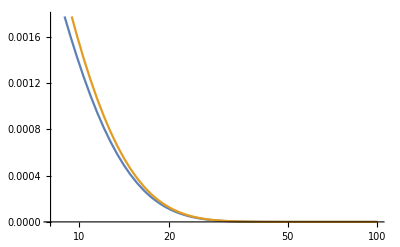

```mathematica
LogLinearPlot[{1/(ⅇ^(2+Ecouple/4+(2 π)/3)+ⅇ^(2-Ecouple/2+(4 π)/3)),ⅇ^(-2-Ecouple/4-(4 π)/3) (1+ⅇ^(2 π/3))},{Ecouple,8,100}]
```

## Not aligned potentials, starting from the neighbouring minima (aligned when offset is zero)

Using τ = τ0 exp(β E), τ0 cancels when looking at ratios

```mathematica
Energy[x_,y_]:=Eo/2(1-Cos[3(x-ϕ)])+E1/2(1-Cos[3y])+Ecouple/2(1-Cos[x-y])-ψo x+ψ1 y
```

```mathematica
EFoF=(Energy[ϕ+π/3,0]-Energy[ϕ,0])//Simplify
```

Eo-(π ψo)/3+1/4 Ecouple Cos[ϕ]+1/4 √3 Ecouple Sin[ϕ]

```mathematica
EFoB=(Energy[ϕ-π/3,0]-Energy[ϕ,0])//Simplify
```

1/6 (6 Eo+2 π ψo+3 Ecouple Cos[ϕ]-3 Ecouple Sin[π/6+ϕ])

```mathematica
EF1F=(Energy[ϕ,π/3]-Energy[ϕ,0])//Simplify
```

1/6 (6 E1+2 π ψ1+3 Ecouple Cos[ϕ]-3 Ecouple Sin[π/6+ϕ])

```mathematica
EF1B=(Energy[ϕ,-π/3]-Energy[ϕ,0])//Simplify
```

E1-(π ψ1)/3+1/4 Ecouple Cos[ϕ]+1/4 √3 Ecouple Sin[ϕ]

```mathematica
Exp[EFoF]/Exp[EF1B]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

```mathematica
Exp[EF1F]/Exp[EFoB]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

```mathematica
Exp[EF1F]/Exp[EFoF]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1+ψo)-1/2 √3 Ecouple Sin[ϕ])

```mathematica
Exp[EFoB]/Exp[EF1B]/.Eo->E1//Simplify
```

ⅇ^(1/3 π (ψ1+ψo)-1/2 √3 Ecouple Sin[ϕ])

```mathematica
tf=1/(1/Exp[EF1F]+1/Exp[EFoF])/.Eo->E1//Simplify;
```

```mathematica
tb=1/(1/Exp[EF1B]+1/Exp[EFoB])/.Eo->E1//Simplify;
```

```mathematica
tf/tb//Simplify
```

ⅇ^(1/3 π (ψ1-ψo))

tFoF/tF1B=  tF1F/tFoB= exp(1/3 β π(ψ1-ψo))

tF1F/tFoF=  tFoB/tF1B = exp(β(1/3 π(ψ1 + ψo)-1/2 Sqrt[3] Ecouple sin(ϕ)))

tF/tB= exp(1/3 β π(ψ1-ψo))